```mathematica
ExpandAll[(x-2)^3]
```

-8+12 x-6 x^2+x^3

```mathematica
(x-2)^3-(x^3+2^3)
```

-8+(-2+x)^3-x^3

```mathematica
Expand[-8+(-2+x)^3-x^3]
```

-16+12 x-6 x^2

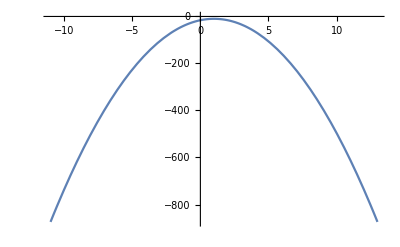

```mathematica
Plot[-16+12 x-6 x^2,{x,-11.,13.}]
```

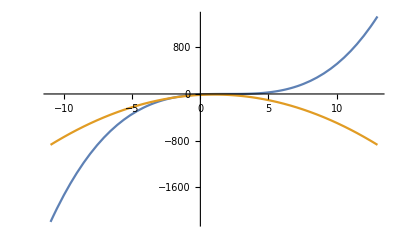

```mathematica
Plot[{-8+12 x-6 x^2+x^3,-16+12 x-6 x^2},{x,-11.,13.}]
```

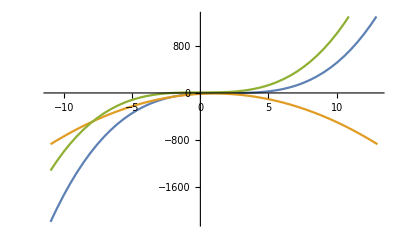

```mathematica
Plot[{-8+12 x-6 x^2+x^3,-16+12 x-6 x^2,(x^3+2^3)},{x,-11.,13.}]
```

```mathematica
(f[x+α]-(f[x]+f[α]))/f[x+α]
```

(-f[x]-f[α]+f[x+α])/f[x+α]

```mathematica
ExpandAll[(f[x+α]-(f[x]+f[α]))/f[x+α]]
```

1-f[x]/f[x+α]-f[α]/f[x+α]

```mathematica
With[{f=D},
ExpandAll[(f[x+α]-(f[x]+f[α]))/f[x+α]]
]
```

0

```mathematica
With[{f=D},
ExpandAll[(f[x]+f[α])/f[x+α]]
]
```

1

```mathematica
With[{f=LaplaceTransform},
ExpandAll[(f[x]+f[α])/f[x+α]]
]
```

LaplaceTransform::argmu: LaplaceTransform called with 1 argument; 3 or more arguments are expected.

General::stop: Further output of LaplaceTransform::argmu will be suppressed during this calculation.

LaplaceTransform[x]/LaplaceTransform[x+α]+LaplaceTransform[α]/LaplaceTransform[x+α]

```mathematica
With[{f=Sin},
ExpandAll[(f[x]+f[α])/f[x+α]]
]
```

Csc[x+α] Sin[x]+Csc[x+α] Sin[α]

```mathematica
With[{f=Function[x,(x-2)^3]},
ExpandAll[(f[x]+f[α])/f[x+α]]
]
```

-16/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)+(12 x)/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)-(6 x^2)/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)+x^3/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)+(12 α)/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)-(6 α^2)/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)+α^3/(-8+12 x-6 x^2+x^3+12 α-12 x α+3 x^2 α-6 α^2+3 x α^2+α^3)

```mathematica
With[{f=Function[x,(x-2)^2]},
ExpandAll[(f[x]+f[α])/f[x+α]]
]
```

8/(4-4 x+x^2-4 α+2 x α+α^2)-(4 x)/(4-4 x+x^2-4 α+2 x α+α^2)+x^2/(4-4 x+x^2-4 α+2 x α+α^2)-(4 α)/(4-4 x+x^2-4 α+2 x α+α^2)+α^2/(4-4 x+x^2-4 α+2 x α+α^2)

```mathematica
Manipulate[Plot[8/(4-4 x+x^2-4 α+2 x α+α^2)-(4 x)/(4-4 x+x^2-4 α+2 x α+α^2)+x^2/(4-4 x+x^2-4 α+2 x α+α^2)-(4 α)/(4-4 x+x^2-4 α+2 x α+α^2)+α^2/(4-4 x+x^2-4 α+2 x α+α^2),{x,-8,8}],{α,-8,8}]
```

```mathematica
Plot3D[8/(4-4 x+x^2-4 α+2 x α+α^2)-(4 x)/(4-4 x+x^2-4 α+2 x α+α^2)+x^2/(4-4 x+x^2-4 α+2 x α+α^2)-(4 α)/(4-4 x+x^2-4 α+2 x α+α^2)+α^2/(4-4 x+x^2-4 α+2 x α+α^2),{x,-8,8},{α,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[
8/(4-4 x+x^2-4 α+2 x α+α^2)-(4 x)/(4-4 x+x^2-4 α+2 x α+α^2)+x^2/(4-4 x+x^2-4 α+2 x α+α^2)-(4 α)/(4-4 x+x^2-4 α+2 x α+α^2)+α^2/(4-4 x+x^2-4 α+2 x α+α^2)
,{x,-8,8},{α,-8,8}
,PlotRange->Full]
```

-Graphics3D-

```mathematica
Grad[8/(4-4 x+x^2-4 α+2 x α+α^2)-(4 x)/(4-4 x+x^2-4 α+2 x α+α^2)+x^2/(4-4 x+x^2-4 α+2 x α+α^2)-(4 α)/(4-4 x+x^2-4 α+2 x α+α^2)+α^2/(4-4 x+x^2-4 α+2 x α+α^2),{x,α}]
```

{-(8 (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)+(4 x (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)-(x^2 (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)+(4 α (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)-(α^2 (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)-4/(4-4 x+x^2-4 α+2 x α+α^2)+(2 x)/(4-4 x+x^2-4 α+2 x α+α^2),-(8 (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)+(4 x (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)-(x^2 (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)+(4 α (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)-(α^2 (-4+2 x+2 α))/((4-4 x+x^2-4 α+2 x α+α^2)^2)-4/(4-4 x+x^2-4 α+2 x α+α^2)+(2 α)/(4-4 x+x^2-4 α+2 x α+α^2)}

```mathematica
Exp[x]==x
```

ⅇ^x==x

```mathematica
Reduce[ⅇ^x==x]
```

C[1]∈ℤ&&x==-ProductLog[C[1],-1]

```mathematica
-ProductLog[1,-1]
```

-ProductLog[1,-1]

```mathematica
-ProductLog[x,-1]
```

-ProductLog[x,-1]

```mathematica
GeneratingFunction[-ProductLog[x,-1],x,x]
```

-GeneratingFunction[ProductLog[x,-1],x,x]

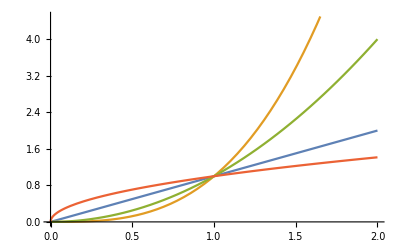

```mathematica
Plot[{x,x^3,x^2,Sqrt[x]},{x,0,2}]
```

```mathematica
Log[x]==x
```

Log[x]==x

```mathematica
Reduce[Log[x]==x]
```

x==ⅇ^(-ProductLog[-1])||x==ⅇ^(-ProductLog[-1,-1])

```mathematica
Plot[ⅇ^(-ProductLog[-1,-1]),{x,-2,2}]
```

-Graphics-

```mathematica
Log[x-ⅇ^(-ProductLog[-1,-1])]
```

Log[-ⅇ^(-ProductLog[-1,-1])+x]

```mathematica
FullSimplify[Log[-ⅇ^(-ProductLog[-1,-1])+x]]
```

Log[x+ProductLog[-1,-1]]

```mathematica
Plot[{Log[x+ProductLog[-1,-1]]},{x,0,2}]
```

-Graphics-

```mathematica
Exp[x]==x
```

ⅇ^x==x

```mathematica
Reduce[ⅇ^x==x]
```

C[1]∈ℤ&&x==-ProductLog[C[1],-1]

```mathematica
Exp[x-ProductLog[1,-1]]
```

ⅇ^(x-ProductLog[1,-1])

```mathematica
Plot[Exp[x-ProductLog[-1]],{x,0,2}]
```

-Graphics-

```mathematica
Sin[x]==x
```

Sin[x]==x

```mathematica
Reduce[Sin[x]==x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Sin[x]==x]

```mathematica
Sin[x]==x∧0<x,1
```

```mathematica
Reduce[Sin[x]==x∧0<x<1,x,Reals]
```

False

```mathematica
Reduce[Sin[x]==x∧-1<x<1,x,Reals]
```

x==0

```mathematica
Sin[x-1]+1
```

1-Sin[1-x]

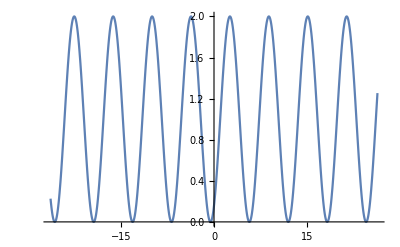

```mathematica
Plot[1-Sin[1-x],{x,-26.389378290154262,26.389378290154262}]
```

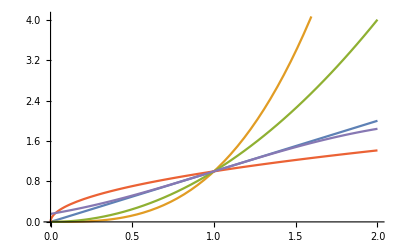

```mathematica
Plot[{x,x^3,x^2,Sqrt[x],Sin[x-1]+1},{x,0,2}]
```